# How to Create Hans Rosling’s Famous Animated Bubble Chart in Wolfram Language

Last week, I came across an interesting Medium article from a Data Science professional I follow. The post walked through creating Hans Rosling’s famous animated bubble chart from one of his Ted Talks regarding how economic prosperity increases life expectancy.

-Graphics-

The article was interesting and helps to showcase the power of various programming languages. In this particular case, the author was utilizing R and cited it’s “range and flexibility”. His final result was an animated version of the ggplot shown below mimicking Rosling’s original above.

-Graphics-

I love R, but love Wolfram Language even more. So, I wanted to try and show off Wolfram Language's capabilities in this area by re-creating his workflow.

### Criteria

The author of the article noted some self-imposed criteria in his workflow:

1.	Can I do it using economic data straight from the World Bank source, without needing to use local data files or package data which may not be up to date?
2.	Can I make it look reasonably close to how Rosling’s chart looked?
3.	Is it possible do to it in a single piped command in R?

I will attempt to follow the exact same criteria, with the exception to #3 where I will use “one line” of Wolfram Language code to create the graphic.

### Grabbing the data

In the article, the author noted the use of a 3rd party library with immediate access to the world bank web API for extracting information. This is a really nice convenience, and one that isn’t quite available in that same form in the Wolfram Language. However, it is worth noting that the Wolfram Language does contain a rather comprehensive built-in knowledge database and in particular there are entries for Country data such as GDP per capita and population. Even life expectancy (the final main piece of information needed for this analysis) is available.

For the purposes of this analysis though, I wanted to keep with the Author’s intention of using the World Bank API, so for that we will utilize Wolfram Language’s URLExecute command, but first we need to acquire a list of countries we want to possibly grab information on.

```mathematica
countries=CanonicalName/@CountryData[]
```

{Afghanistan,AlandIslands,Albania,Algeria,AmericanSamoa,Andorra,Angola,Anguilla,AntiguaBarbuda,Argentina,Armenia,Aruba,Australia,Austria,Azerbaijan,Bahamas,Bahrain,Bangladesh,Barbados,Belarus,Belgium,Belize,Benin,Bermuda,Bhutan,Bolivia,BonaireSintEustatiusAndSaba,BosniaHerzegovina,Botswana,BouvetIsland,Brazil,BritishIndianOceanTerritory,BritishVirginIslands,Brunei,Bulgaria,BurkinaFaso,Burundi,Cambodia,Cameroon,Canada,CapeVerde,CaymanIslands,CentralAfricanRepublic,Chad,Chile,China,ChristmasIsland,CocosKeelingIslands,Colombia,Comoros,CookIslands,CostaRica,Croatia,Cuba,Curacao,Cyprus,CzechRepublic,DemocraticRepublicCongo,Denmark,Djibouti,Dominica,DominicanRepublic,EastTimor,Ecuador,Egypt,ElSalvador,EquatorialGuinea,Eritrea,Estonia,Ethiopia,FalklandIslands,FaroeIslands,Fiji,Finland,France,FrenchGuiana,FrenchPolynesia,FrenchSouthernAndAntarcticLands,Gabon,Gambia,GazaStrip,Georgia,Germany,Ghana,Gibraltar,Greece,Greenland,Grenada,Guadeloupe,Guam,Guatemala,Guernsey,Guinea,GuineaBissau,Guyana,Haiti,Honduras,HongKong,Hungary,Iceland,India,Indonesia,Iran,Iraq,Ireland,IsleOfMan,Israel,Italy,IvoryCoast,Jamaica,Japan,Jersey,Jordan,Kazakhstan,Kenya,Kiribati,Kosovo,Kuwait,Kyrgyzstan,Laos,Latvia,Lebanon,Lesotho,Liberia,Libya,Liechtenstein,Lithuania,Luxembourg,Macau,Macedonia,Madagascar,Malawi,Malaysia,Maldives,Mali,Malta,MarshallIslands,Martinique,Mauritania,Mauritius,Mayotte,Mexico,Micronesia,Moldova,Monaco,Mongolia,Montenegro,Montserrat,Morocco,Mozambique,Myanmar,Namibia,Nauru,Nepal,Netherlands,NewCaledonia,NewZealand,Nicaragua,Niger,Nigeria,Niue,NorfolkIsland,NorthernMarianaIslands,NorthKorea,Norway,Oman,Pakistan,Palau,Panama,PapuaNewGuinea,Paraguay,Peru,Philippines,PitcairnIslands,Poland,Portugal,PuertoRico,Qatar,RepublicCongo,Reunion,Romania,Russia,Rwanda,SaintBarthelemy,SaintHelena,SaintKittsNevis,SaintLucia,SaintMartin,SaintPierreMiquelon,SaintVincentGrenadines,Samoa,SanMarino,SaoTomePrincipe,SaudiArabia,Senegal,Serbia,Seychelles,SierraLeone,Singapore,SintMaarten,Slovakia,Slovenia,SolomonIslands,Somalia,SouthAfrica,SouthGeorgiaAndTheSouthSandwichIslands,SouthKorea,SouthSudan,Spain,SriLanka,Sudan,Suriname,Svalbard,Swaziland,Sweden,Switzerland,Syria,Taiwan,Tajikistan,Tanzania,Thailand,Togo,Tokelau,Tonga,TrinidadTobago,Tunisia,Turkey,Turkmenistan,TurksCaicosIslands,Tuvalu,Uganda,Ukraine,UnitedArabEmirates,UnitedKingdom,UnitedStates,UnitedStatesMinorOutlyingIslands,UnitedStatesVirginIslands,Uruguay,Uzbekistan,Vanuatu,VaticanCity,Venezuela,Vietnam,WallisFutuna,WestBank,WesternSahara,Yemen,Zambia,Zimbabwe}

The World Bank API’s prefer to deal explicitly with 2 letter country codes when referencing a particular country, so for that I will again utilize Wolfram’s knowledge base first to generate that for each country.

```mathematica
countryCodes=AssociationThread[Function[CountryData[#,"CountryCode"]]/@countries,countries]//KeySelect[MissingQ/*Not]
```

<|AF→Afghanistan,AX→AlandIslands,AL→Albania,DZ→Algeria,AS→AmericanSamoa,AD→Andorra,AO→Angola,AI→Anguilla,AG→AntiguaBarbuda,AR→Argentina,AM→Armenia,AW→Aruba,AU→Australia,AT→Austria,AZ→Azerbaijan,BS→Bahamas,BH→Bahrain,BD→Bangladesh,BB→Barbados,BY→Belarus,BE→Belgium,BZ→Belize,BJ→Benin,BM→Bermuda,BT→Bhutan,BO→Bolivia,BQ→BonaireSintEustatiusAndSaba,BA→BosniaHerzegovina,BW→Botswana,BV→BouvetIsland,BR→Brazil,IO→BritishIndianOceanTerritory,VG→BritishVirginIslands,BN→Brunei,BG→Bulgaria,BF→BurkinaFaso,BI→Burundi,KH→Cambodia,CM→Cameroon,CA→Canada,CV→CapeVerde,KY→CaymanIslands,CF→CentralAfricanRepublic,TD→Chad,CL→Chile,CN→China,CX→ChristmasIsland,CC→CocosKeelingIslands,CO→Colombia,KM→Comoros,CK→CookIslands,CR→CostaRica,HR→Croatia,CU→Cuba,CW→Curacao,CY→Cyprus,CZ→CzechRepublic,CD→DemocraticRepublicCongo,DK→Denmark,DJ→Djibouti,DM→Dominica,DO→DominicanRepublic,TL→EastTimor,EC→Ecuador,EG→Egypt,SV→ElSalvador,GQ→EquatorialGuinea,ER→Eritrea,EE→Estonia,ET→Ethiopia,FK→FalklandIslands,FO→FaroeIslands,FJ→Fiji,FI→Finland,FR→France,GF→FrenchGuiana,PF→FrenchPolynesia,TF→FrenchSouthernAndAntarcticLands,GA→Gabon,GM→Gambia,GZ→GazaStrip,GE→Georgia,DE→Germany,GH→Ghana,GI→Gibraltar,GR→Greece,GL→Greenland,GD→Grenada,GP→Guadeloupe,GU→Guam,GT→Guatemala,GG→Guernsey,GN→Guinea,GW→GuineaBissau,GY→Guyana,HT→Haiti,HN→Honduras,HK→HongKong,HU→Hungary,IS→Iceland,IN→India,ID→Indonesia,IR→Iran,IQ→Iraq,IE→Ireland,IM→IsleOfMan,IL→Israel,IT→Italy,CI→IvoryCoast,JM→Jamaica,JP→Japan,JE→Jersey,JO→Jordan,KZ→Kazakhstan,KE→Kenya,KI→Kiribati,KW→Kuwait,KG→Kyrgyzstan,LA→Laos,LV→Latvia,LB→Lebanon,LS→Lesotho,LR→Liberia,LY→Libya,LI→Liechtenstein,LT→Lithuania,LU→Luxembourg,MO→Macau,MK→Macedonia,MG→Madagascar,MW→Malawi,MY→Malaysia,MV→Maldives,ML→Mali,MT→Malta,MH→MarshallIslands,MQ→Martinique,MR→Mauritania,MU→Mauritius,YT→Mayotte,MX→Mexico,FM→Micronesia,MD→Moldova,MC→Monaco,MN→Mongolia,ME→Montenegro,MS→Montserrat,MA→Morocco,MZ→Mozambique,MM→Myanmar,NA→Namibia,NR→Nauru,NP→Nepal,NL→Netherlands,NC→NewCaledonia,NZ→NewZealand,NI→Nicaragua,NE→Niger,NG→Nigeria,NU→Niue,NF→NorfolkIsland,MP→NorthernMarianaIslands,KP→NorthKorea,NO→Norway,OM→Oman,PK→Pakistan,PW→Palau,PA→Panama,PG→PapuaNewGuinea,PY→Paraguay,PE→Peru,PH→Philippines,PN→PitcairnIslands,PL→Poland,PT→Portugal,PR→PuertoRico,QA→Qatar,CG→RepublicCongo,RE→Reunion,RO→Romania,RU→Russia,RW→Rwanda,BL→SaintBarthelemy,SH→SaintHelena,KN→SaintKittsNevis,LC→SaintLucia,MF→SaintMartin,PM→SaintPierreMiquelon,VC→SaintVincentGrenadines,WS→Samoa,SM→SanMarino,ST→SaoTomePrincipe,SA→SaudiArabia,SN→Senegal,RS→Serbia,SC→Seychelles,SL→SierraLeone,SG→Singapore,SX→SintMaarten,SK→Slovakia,SI→Slovenia,SB→SolomonIslands,SO→Somalia,ZA→SouthAfrica,GS→SouthGeorgiaAndTheSouthSandwichIslands,KR→SouthKorea,SS→SouthSudan,ES→Spain,LK→SriLanka,SD→Sudan,SR→Suriname,SJ→Svalbard,SZ→Swaziland,SE→Sweden,CH→Switzerland,SY→Syria,TW→Taiwan,TJ→Tajikistan,TZ→Tanzania,TH→Thailand,TG→Togo,TK→Tokelau,TO→Tonga,TT→TrinidadTobago,TN→Tunisia,TR→Turkey,TM→Turkmenistan,TC→TurksCaicosIslands,TV→Tuvalu,UG→Uganda,UA→Ukraine,AE→UnitedArabEmirates,GB→UnitedKingdom,US→UnitedStates,UM→UnitedStatesMinorOutlyingIslands,VI→UnitedStatesVirginIslands,UY→Uruguay,UZ→Uzbekistan,VU→Vanuatu,VA→VaticanCity,VE→Venezuela,VN→Vietnam,WF→WallisFutuna,WE→WestBank,EH→WesternSahara,YE→Yemen,ZM→Zambia,ZW→Zimbabwe|>

Before getting any data on the particular countries, the last identifying piece of information we want for the plot later is the region of a particular country so that we can perform grouping within the plot. To get this, I’ll make a call to the World Bank API passing in the country code and then retrieving the reported region.

```mathematica
countryRegions=countryCodes//
	Keys//
	Map[Function[URLExecute["http://api.worldbank.org/v2/country/"<>#<>"?format=json","RawJSON"][[2,1,"region","value"]]]]//
	Quiet//
	Function[AssociationThread[Keys[countryCodes],#]]//
	Select[StringQ];
```

After deleting any countries that may have failed due to being unrecognized by the API, I will next plot the number of countries by region to ensure we have successfully retrieved the data as well as to get a sense for areas with the most countries.

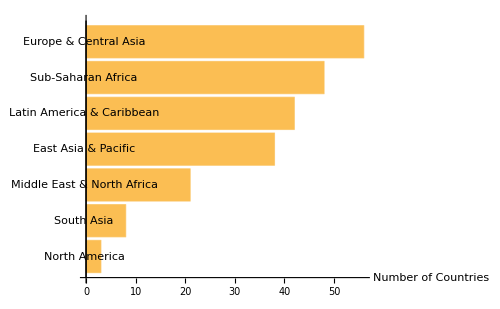

```mathematica
countryRegions//
	Counts//
	Sort//
	Function[BarChart[#,ChartLabels->Automatic,AxesLabel->"Number of Countries",ImageSize->500,BarOrigin->Left]]
```

The author of the original article provided the 3 indicators that we need to pass into the World Bank API in order to get our required information. Those are shown below and will provide us with Life Expectancy, GDP Per Capita, and Total Population.

```mathematica
indicators={"SP.DYN.LE00.IN","NY.GDP.PCAP.CD","SP.POP.TOTL"}
```

{SP.DYN.LE00.IN,NY.GDP.PCAP.CD,SP.POP.TOTL}

We’ll now use the World Bank’s API, passing in the above indicators and retrieving information for each country in our list from the years 1960 to 2000.

```mathematica
rosling=Table[URLExecute["http://api.worldbank.org/v2/country/"<>country<>"/indicator/"<>StringRiffle[indicators,";"],{
	"format"->"json",
	"source"->2,
	"date"->"1960:2020",
	"per_page"->2000,
	"frequency"->"Y",
	"page"->1
},"RawJSON"],{country,Keys[countryRegions]}];
```

Next, I’ll save the data so I don’t have to retrieve it via the API again if I close my work and pick back up later.

```mathematica
Put[rosling,FileNameJoin[{NotebookDirectory[],"rosling.m"}]];
```

Retrieving the data can then be performed using the Get[] function.

```mathematica
rosling=Get[FileNameJoin[{NotebookDirectory[],"rosling.m"}]];
```

Now we need to combine the data taking only the properties we’re interested in. Then, we’ll do some rearranging to get it into a more “tidy” format.

```mathematica
rosling=rosling//
	Flatten//
	DeleteCases[Null]//
	Select[KeyExistsQ["indicator"]]//
	GroupBy[Function[{#[["country","value"]],#[["country","id"]],ToExpression[#date]}]->Function[#[["value"]]]]//
	KeyValueMap[Function[{key,value},AssociationThread[
		{"Country","CountryCode","Year","LifeExpectancy","GDPperCapita","Population"},
		Join[key,value]
	]]];
```

Finally, the region information is the only parameters missing from what was extracted in the API calls, so I will add that back in manually.

```mathematica
rosling=rosling//
	Map[Function[Insert[#,"Region"->countryRegions[#CountryCode],3]]]//
	Select[Function[!MissingQ[#Region]]];
```

```mathematica
rosling[[All,"Region"]]//DeleteDuplicates
```

{South Asia,Europe & Central Asia,Middle East & North Africa,East Asia & Pacific,Sub-Saharan Africa ,Latin America & Caribbean ,North America}

After evaluation, I end up with the following clean data set for making my graphics.

```mathematica
Dataset[rosling,MaxItems->10,ItemSize->10]
```

Dataset[<>]

### Creating a static chart for a single year

Next, I’ll create a function capable of being passed a single year and creating a graphic showing the GDP per capita on the x-axis (plotted on a log scale) and the life expectancy on the y-axis where the size of the bubbles is used to indicate the countries population.

```mathematica
createPlot[year_]:=With[{
	populationsMinMax=rosling[[All,"Population"]]//Select[NumericQ]//MinMax,
	gdpMinMax=rosling[[All,"GDPperCapita"]]//Select[NumericQ]//MinMax,
	lifeMinMax=rosling[[All,"LifeExpectancy"]]//Select[NumericQ]//MinMax
	},
	rosling//
		Select[Function[#Year==year]]//
		GroupBy[{Function[#Region],Function[#Country]->Function[{#GDPperCapita,#LifeExpectancy,#Population}]}]//
		Map[Map[First]]//
		Map[KeySort]//
		Map[Select[AllTrue[NumericQ]]]//
		KeyTake[Keys[Sort[Counts[countryRegions]]]]//
		Function[Rasterize@BubbleChart[#,PlotLabel->year,LabelStyle->Directive[14],ImageSize->400,FrameLabel->{"GDP Per Capita","Life Expectancy"},ChartLegends->Automatic,ScalingFunctions->{"Log",Identity},PlotRange->{Log@gdpMinMax,lifeMinMax}]]
]
```

Here are examples of the function in action below.

```mathematica
createPlot[1960]
createPlot[2020]
```

-Graphics-

-Graphics-

### Animating the chart

With a single function (and line of code) we are now able to make a plot for a particular year, the only remaining step is to create all the plots across all the years and then export the resulting images as a GIF!

```mathematica
plots=createPlot/@Range[1960,2020];
```

```mathematica
ListAnimate[plots]
```

```mathematica
Export["Downloads/hans_rosling.gif",plots]
```

Downloads/hans_rosling.gif